```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["preliminaryData.txt","Data"];
```

```mathematica
data = Flatten[data];
```

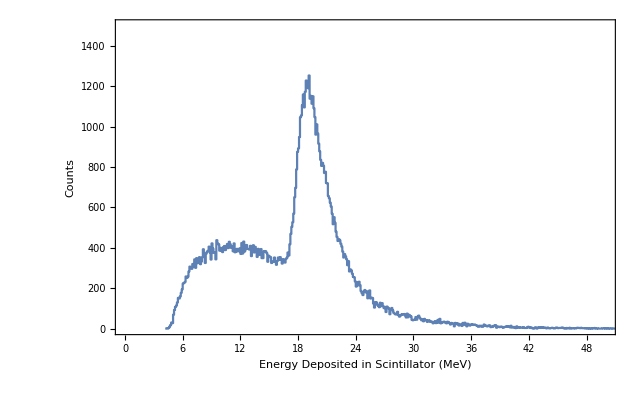

100000

17.25

6.17039

```mathematica
hist=HistogramList[data,{.1}];

ListPlot[Transpose[{hist[[1]],ArrayPad[hist[[2]],{0,1},"Fixed"]}],InterpolationOrder->0,Joined->True,AxesOrigin->{0,0},PlotRange->{{0,50},{0,1500}},RotateLabel->True,FrameLabel->{Style["Energy Deposited in Scintillator (MeV)",20,Bold,Blue],Style["Counts",20,Bold,Blue]},
LabelStyle->Directive[Blue,Bold],Frame->True]
Length[dataE]
Mean[dataE]
StandardDeviation[dataE]
```